```mathematica
Constructing 3-dimentional (correlated) BM
```

```mathematica
A={{1,0,0},{Subscript[ρ, 2,1],Sqrt[1-Subscript[ρ, 2,1]^2],0},{Subscript[ρ, 3,1],x,y}};
A.Transpose[A]=={{1,Subscript[ρ, 2,1],Subscript[ρ, 3,1]},{Subscript[ρ, 2,1],1,Subscript[ρ, 3,2]},{Subscript[ρ, 3,1],Subscript[ρ, 3,2],1}}//TraditionalForm
AA=A/.Solve[{Sqrt[1-Subscript[ρ, 2,1]^2]x+Subscript[ρ, 2,1] Subscript[ρ, 3,1]==Subscript[ρ, 3,2],Subscript[ρ, 3,1]^2+x^2+y^2==1},{x,y}][[2]]//Simplify
AA//TraditionalForm
```

(1 | ρ_(2,1) | ρ_(3,1)
ρ_(2,1) | 1 | √(1-ρ_(2,1)^2) x+ρ_(2,1) ρ_(3,1)
ρ_(3,1) | √(1-ρ_(2,1)^2) x+ρ_(2,1) ρ_(3,1) | x^2+y^2+ρ_(3,1)^2)==(1 | ρ_(2,1) | ρ_(3,1)
ρ_(2,1) | 1 | ρ_(3,2)
ρ_(3,1) | ρ_(3,2) | 1)

{{1,0,0},{ρ_(2,1),√(1-ρ_(2,1)^2),0},{ρ_(3,1),(-ρ_(2,1) ρ_(3,1)+ρ_(3,2))/(√(1-ρ_(2,1)^2)),√((-1+ρ_(2,1)^2+ρ_(3,1)^2-2 ρ_(2,1) ρ_(3,1) ρ_(3,2)+ρ_(3,2)^2)/(-1+ρ_(2,1)^2))}}

(1 | 0 | 0
ρ_(2,1) | √(1-ρ_(2,1)^2) | 0
ρ_(3,1) | (ρ_(3,2)-ρ_(2,1) ρ_(3,1))/(√(1-ρ_(2,1)^2)) | √((ρ_(2,1)^2-2 ρ_(3,1) ρ_(3,2) ρ_(2,1)+ρ_(3,1)^2+ρ_(3,2)^2-1)/(ρ_(2,1)^2-1)))

```mathematica
CC=AA/.{Subscript[ρ, 2,1]-> -.5,Subscript[ρ, 3,1]-> -.7,Subscript[ρ, 3,2]-> .4}
```

{{1,0,0},{-0.5,0.866025,0},{-0.7,0.057735,0.711805}}

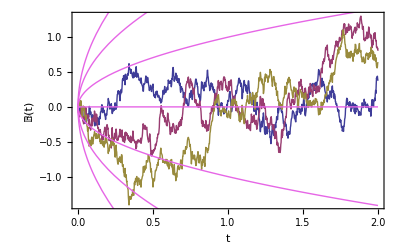

```mathematica
dim=3;
t1=2;k=1000;
dt=t1/k//N;
dB:=Sqrt[dt]Table[Random[NormalDistribution[]],{k}];
dBB=Table[Sqrt[dt]CC.Table[Random[NormalDistribution[]],{dim}],{k}];
F[{t_,B_},dB_]:={t+dt,B+dB}
BB=FoldList[F,{0,Table[0,{dim}]},dBB];
Show[
ListPlot[
Table[Transpose[{Transpose[BB][[1]],Transpose[Transpose[BB][[2]]][[i]]}],{i,dim}],Joined-> True,Frame-> True,FrameLabel-> {t,𝔹[t]}],
Plot[Table[k Sqrt[t],{k,-3,3}],{t,0,t1},
PlotStyle-> RGBColor[.9,.4,.9]]]
```